```mathematica
Get["DMTestFunctions`"]
Get["DifferenceMapOptimizer`"]
Get["DMData`"]
```

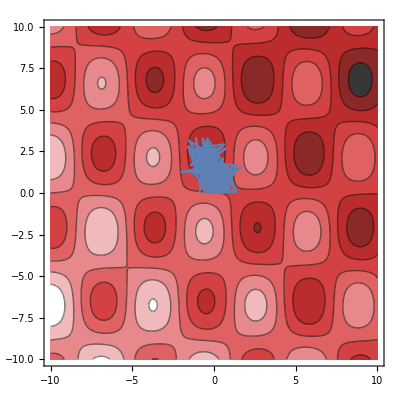
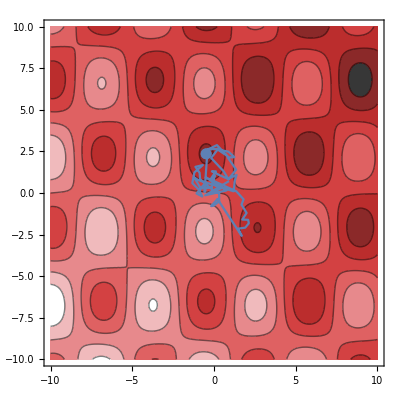
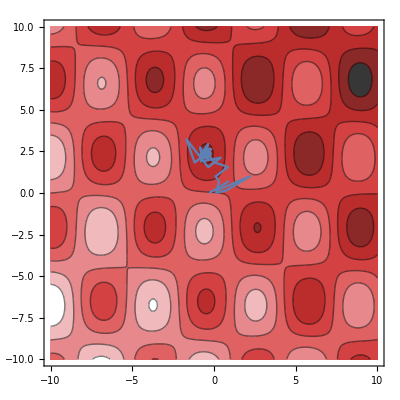
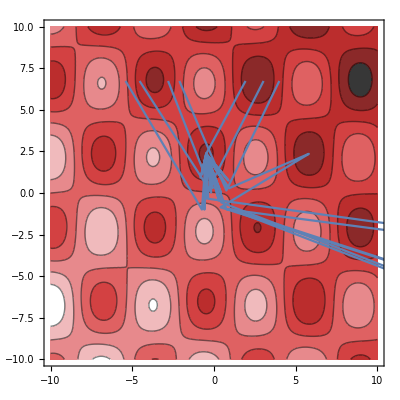
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Automatic | SimulatedAnnealing | DifferentialEvolution | NelderMead | RandomSearch

```mathematica
builtinMethods = {Automatic, "SimulatedAnnealing", "DifferentialEvolution", "NelderMead", "RandomSearch"};
vars = {x, y};
offset = {100, 100};
range = Sequence[{x, -10, 10}, {y, -10, 10}];
nicePlot[method_] := Module[{fun, solution, minima},
{{fun, solution}, {minima}} =
Reap[
NMinimize[
griewankN[vars - offset],
vars, 
EvaluationMonitor-> Hold[Sow[vars]], 
Method->method, 
MaxIterations->100]
];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True], 
ListPlot[{Map[# /. solution &, vars]}]
]
];
Grid[{Map[nicePlot, builtinMethods], builtinMethods}]
```

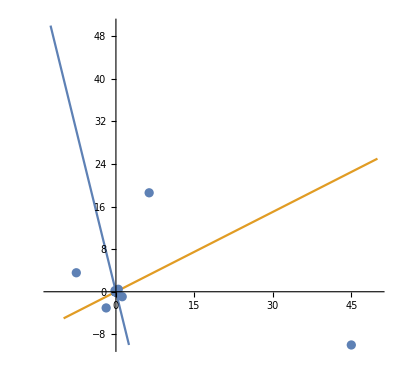

```mathematica
C1 = {-0.25, 1.0};
C2 = {1.0, 0.5};
P1 = Projection[#, C1] &;
P2 = Projection[#, C2] &;
β = 2.0;
f1 = (1 - 1/β) P1[#] + (1/β) # &;
f2 = (1 + 1/β) P2[#] - (1/β) # &;
f = #+ β(P1[f2[#]] - P2[f1[#]]) &;
DM[x_, it_] := Module[{t, i},
t = x;
For[i = 0, i < it, i++, t = Sow[f[t]]];
Return[t];
];
start = {45, -10};
{solution, {steps}} = Reap[DM[start, 50]];
Show[ParametricPlot[{u C1, u C2}, {u, -10, 50}], ListPlot[Prepend[steps, start]]]
```

```mathematica
C1 = {-0.25, 1.0, 2.25};
C2 = {1.0, 0.5, -0.25};
P1 = Projection[#, C1] &;
P2 = Projection[#, C2] &;
β = 2.5;
f1 = (1 - 1/β) P1[#] + (1/β) # &;
f2 = (1 + 1/β) P2[#] - (1/β) # &;
f = #+ β(P1[f2[#]] - P2[f1[#]]) &;
DM[x_, it_] := Module[{t, i},
t = x;
For[i = 0, i < it, i++, t = Sow[f[t]]];
Return[t];
];
start = {5, -10, 7};
{solution, {steps}} = Reap[DM[start, 15]];
Show[ParametricPlot3D[{u C1, u C2}, {u, -10, 45}], ListPointPlot3D[Prepend[steps, start], DataRange->Automatic]]
```

```mathematica
start = {4, 7};
other = {7, 8};
fun = N[griewankN[start]];
{fun2, solution} = FindMinimum[griewankN[{x, y}], {x, 4}, {y, 7}];
sol = {x, y} /. solution
Show[Plot3D[griewankN[{x, y}], {x, -10, 10}, {y, -10, 10}], ListPointPlot3D[{Join[start, {fun+0.01}],  Join[sol, {fun2+0.02}], Append[other, griewankN[other]]}]]
```

{3.14002,4.43844}

-Graphics3D-

```mathematica
dmSettings = <|
"dim" -> 3,
"niter" -> 100,
"tolerance" -> 1 10^-8,
"runCount" -> 20,
"innerNiter" -> 65,
"secondPointDistance" -> 5.0,
"solversToDo" -> {"dm"}
|>;
dmResults = makeResults[dmSettings];
```

```mathematica
Export["dmresults.json", dmResults, "JSON"]
```

dmresults.json

```mathematica
as = ToAssociations[dmResults];
```

```mathematica
as[["dm"]][["griewank"]]
```

{<|iterate→{{704.147,438.368,110.373},{699.824,426.448,113.543},{699.856,100.765,246.447},{667.671,89.6691,239.656},94,{12820.3,13638.2,-14941.},{12820.3,13875.2,-15125.6},{12607.2,13724.6,-15168.1}},5,nfev→21345|>,19}
 |  |  |  |

```mathematica
builtinSettings = <|
"dim" -> 4,
"niter" -> 1000,
"tolerance" -> 1 10^-8,
"runCount" -> 50,
"innerNiter" -> 60,
"secondPointDistance" -> 5.0,
"solversToDo" -> {"sa", "de", "nm", "rs"}
|>;
builtinResults = makeResults[builtinSettings];
```

```mathematica
as = ToAssociations[builtinResults];
Length[as[["nm"]][["griewank"]][[1]][["iterate"]]]
```

```mathematica
as
```

```mathematica
Reap[NMinimize[griewankN @ vars, vars, MaxIterations -> 1000, EvaluationMonitor-> Hold[Sow[1]]]][[2]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,19801,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}
 |  |  |  |

```mathematica
ToAssociations[rules_] := Replace[rules, x : {__Rule} :> Association[x], {0, Infinity}];
```

```mathematica
as
```

<|sa→<|griewank→{1},4,ackley→{<|fun→18.131,x→{0.239754,2,19},1,iterate→{{0.643476,0.766972,0.280303,0.964763},{-0.00195532,-0.211385,0.93601,-0.293238},109,{0.239754,0.332187,-1.11843,0.745222}}|>,49}|>,2,rs→<|1|>|>
 |  |  |  |

```mathematica
stats = ToAssociations[
Map[
Function[s,
s -> Map[
Function[r,
r -> With[{
funvs = Map[#["fun"] &, as[s][r]],
nfevs = Map[#["nfev"] &, as[s][r]]},
{"averageSolution" -> (Plus @@ funvs) / Length[funvs],
"medianSolution" -> Median@funvs,
"minimumSolution" -> Min @@ funvs,
"averageNfevs" -> N[(Plus @@ nfevs) / Length[nfevs]],
"medianNfevs" -> N[Median @ nfevs],
"minimumNfevs" -> N[Min @@ nfevs]
}]
], 
testFunctions[[;;,1]]]], 
(* Don't include the `auto` method in the analysis since we don't collect data for it by default.
The automatic method is just DifferentialEvolution or NelderMead, depending on the situation. *)
builtinSettings["solversToDo"]
]
];
```

```mathematica
stats
```

```mathematica
testResults = ToAssociations[
makeResults[
<|
"dim" -> 4,
"niter" -> 1000,
"runCount" -> 3,
"innerNiter" -> 65,
"secondPointDistance" -> 5,
"solversToDo" -> {"sa"}
|>
]
];
```

1000

griewankN[{xx[1],xx[2],xx[3],xx[4]}]

112

1000

griewankN[{xx[1],xx[2],xx[3],xx[4]}]

112

1000

griewankN[{xx[1],xx[2],xx[3],xx[4]}]

112

1000

rosenbrockN[{xx[1],xx[2],xx[3],xx[4]}]

3333

1000

rosenbrockN[{xx[1],xx[2],xx[3],xx[4]}]

3333

1000

rosenbrockN[{xx[1],xx[2],xx[3],xx[4]}]

3333

1000

schwefelN[{xx[1],xx[2],xx[3],xx[4]}]

8011

1000

schwefelN[{xx[1],xx[2],xx[3],xx[4]}]

8011

1000

schwefelN[{xx[1],xx[2],xx[3],xx[4]}]

8011

1000

schafferN[{xx[1],xx[2],xx[3],xx[4]}]

92

1000

schafferN[{xx[1],xx[2],xx[3],xx[4]}]

92

1000

schafferN[{xx[1],xx[2],xx[3],xx[4]}]

92

1000

ackleyN[{xx[1],xx[2],xx[3],xx[4]}]

123

1000

ackleyN[{xx[1],xx[2],xx[3],xx[4]}]

123

1000

ackleyN[{xx[1],xx[2],xx[3],xx[4]}]

123

```mathematica
testResults[["sa"]][["griewank"]][[1]][["nfev"]]
```

112

```mathematica
Length[Reap[NMinimize[griewankN @ vars, vars, MaxIterations -> 1000, EvaluationMonitor-> Hold[Sow[vars]]]][[2]][[1]]]
```

20044

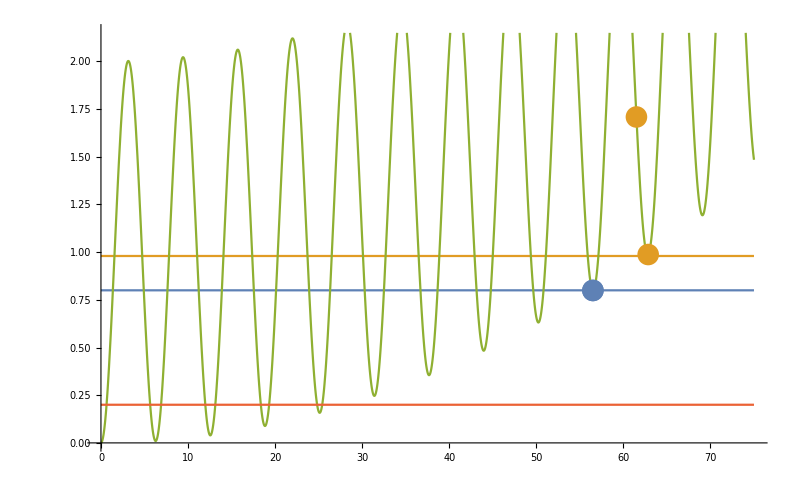

```mathematica
Show[
Plot[{0.8, 0.98, griewankN @ {xi}, 0.2}, {xi, 0, 75}],
ListPlot[{{{56.5, griewankN @ {56.5}}}, {{61.5, griewankN @ {61.5}}, {62.85, griewankN @ {62.85}}}}]
]
```